## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet",}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L0BPhaseSet,L1PhaseSet,L2PhaseSet,L3PhaseSet}

### Sigma

```mathematica
fitVar = "PDrive_sigmaSI90_z"
```

PDrive_sigmaSI90_z

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

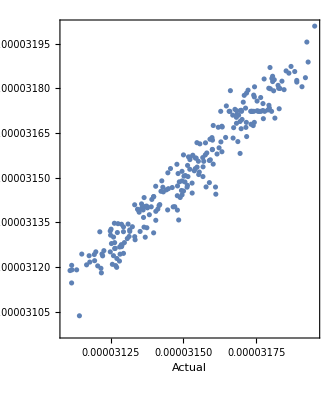

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
L0BPhaseSet | 1 | 1.14582×10^-12 | 1.14582×10^-12 | 443.931 | 1.69104×10^-56
L1PhaseSet | 1 | 6.56267×10^-12 | 6.56267×10^-12 | 2542.62 | 1.0513×10^-129
L2PhaseSet | 1 | 2.26733×10^-12 | 2.26733×10^-12 | 878.445 | 3.58866×10^-82
L3PhaseSet | 1 | 2.03719×10^-15 | 2.03719×10^-15 | 0.789283 | 0.375207
Error | 240 | 6.19456×10^-13 | 2.58107×10^-15 |  | 
Total | 244 | 1.05973×10^-11 |  |  |

```mathematica
lmSigma = lm;
```

### Spacing

```mathematica
fitVar = "bunchSpacing"
```

bunchSpacing

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

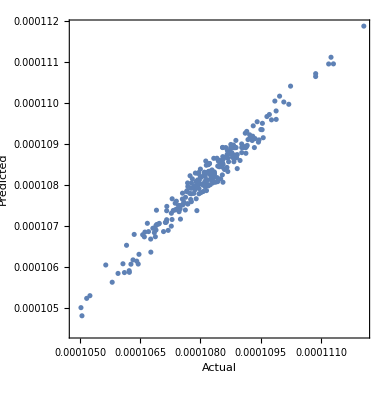

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
L0BPhaseSet | 1 | 2.15875×10^-11 | 2.15875×10^-11 | 486.425 | 1.20229×10^-59
L1PhaseSet | 1 | 1.41258×10^-10 | 1.41258×10^-10 | 3182.94 | 1.67692×10^-140
L2PhaseSet | 1 | 1.14078×10^-10 | 1.14078×10^-10 | 2570.5 | 3.17588×10^-130
L3PhaseSet | 1 | 2.99436×10^-16 | 2.99436×10^-16 | 0.00674713 | 0.934603
Error | 240 | 1.06512×10^-11 | 4.43798×10^-14 |  | 
Total | 244 | 2.87576×10^-10 |  |  |

```mathematica
lmSpacing = lm;
```

## Solve

```mathematica
lm["Properties"]
```

{AdjustedRSquared,AIC,AICc,ANOVATable,ANOVATableDegreesOfFreedom,ANOVATableEntries,ANOVATableFStatistics,ANOVATableMeanSquares,ANOVATablePValues,ANOVATableSumsOfSquares,BasisFunctions,BetaDifferences,BestFit,BestFitParameters,BIC,CatcherMatrix,CoefficientOfVariation,CookDistances,CorrelationMatrix,CovarianceMatrix,CovarianceRatios,Data,DesignMatrix,DurbinWatsonD,EigenstructureTable,EigenstructureTableEigenvalues,EigenstructureTableEntries,EigenstructureTableIndexes,EigenstructureTablePartitions,EstimatedVariance,FitDifferences,FitResiduals,Function,FVarianceRatios,HatDiagonal,MeanPredictionBands,MeanPredictionConfidenceIntervals,MeanPredictionConfidenceIntervalTable,MeanPredictionConfidenceIntervalTableEntries,MeanPredictionErrors,ParameterConfidenceIntervals,ParameterConfidenceIntervalTable,ParameterConfidenceIntervalTableEntries,ParameterConfidenceRegion,ParameterErrors,ParameterPValues,ParameterTable,ParameterTableEntries,ParameterTStatistics,PartialSumOfSquares,PredictedResponse,Properties,Response,RSquared,SequentialSumOfSquares,SingleDeletionVariances,SinglePredictionBands,SinglePredictionConfidenceIntervals,SinglePredictionConfidenceIntervalTable,SinglePredictionConfidenceIntervalTableEntries,SinglePredictionErrors,StandardizedResiduals,StudentizedResiduals,VarianceInflationFactors}

```mathematica
lm["BestFit"]
```

-0.000152011+0.0000145448 L0BPhaseSet+0.0000493925 L1PhaseSet-0.000033676 L2PhaseSet+1.30837×10^-7 L3PhaseSet

```mathematica
allowedDeltaFromNominal = 2;
sol = NMinimize[{
lmSigma["BestFit"],
lmSpacing["BestFit"] >140*^-6 &&
lmSpacing["BestFit"] <160*^-6 && 
L0BPhaseSet>-allowedDeltaFromNominal&& 
L0BPhaseSet<allowedDeltaFromNominal&& 
L3PhaseSet>-allowedDeltaFromNominal&& 
L3PhaseSet<allowedDeltaFromNominal&& 
L1PhaseSet>(-20-allowedDeltaFromNominal)&& 
L1PhaseSet<(-20+allowedDeltaFromNominal)&& 
L2PhaseSet>(-40-allowedDeltaFromNominal)&& 
L2PhaseSet<(-40+allowedDeltaFromNominal)
},
{L0BPhaseSet, L1PhaseSet, L2PhaseSet, L3PhaseSet}
]
```

{0.0000108177,{L0BPhaseSet→-2.,L1PhaseSet→-22.,L2PhaseSet→-42.,L3PhaseSet→2.}}

```mathematica
lmSigma["BestFit"]/.sol[[2]]
```

0.0000108177

Closest point in the dataset

```mathematica
MinimalBy[
raw,
(#L0BPhaseSet -(L0BPhaseSet&/@sol[[2]]) )^2+(#L1PhaseSet -(L1PhaseSet&/@sol[[2]]) )^2+(#L2PhaseSet -(L2PhaseSet&/@sol[[2]]) )^2+(#L3PhaseSet -(L3PhaseSet&/@sol[[2]]) )^2&
]
```

{<|L0BPhaseSet→1.97048,L1PhaseSet→-21.2513,L2PhaseSet→-38.0331,L3PhaseSet→1.98547,S1EL_xOffset→0.00211528,S1EL_yOffset→0.0000955914,S2EL_xOffset→-0.00233526,S2EL_yOffset→0.000215055,S2ER_xOffset→-0.00140082,S2ER_yOffset→-0.000348374,S1ER_xOffset→0.00377853,S1ER_yOffset→-0.00024014,XC1FFkG→0.0542009,XC3FFkG→-0.0165816,YC1FFkG→0.00481707,YC2FFkG→-0.0450738,PDrive_mean_x→6.0901×10^-6,PDrive_mean_y→0.0000362749,PDrive_sigma_x→0.0000424124,PDrive_sigma_y→0.0000310877,PDrive_mean_xp→0.000134382,PDrive_mean_yp→-0.00016886,PDrive_median_x→-2.806×10^-7,PDrive_median_y→0.0000344113,PDrive_median_xp→0.000249537,PDrive_median_yp→-0.000170895,PDrive_sigmaSI90_x→0.0000310108,PDrive_sigmaSI90_y→0.0000252129,PDrive_sigmaSI90_z→0.0000315525,PDrive_emitSI90_x→0.000132619,PDrive_emitSI90_y→9.4199×10^-6,PDrive_zCentroid→991.332,PWitness_mean_x→7.8754×10^-6,PWitness_mean_y→-0.0000180247,PWitness_sigma_x→0.0000222815,PWitness_sigma_y→0.0000229424,PWitness_mean_xp→-0.0000328381,PWitness_mean_yp→-0.000200348,PWitness_median_x→7.8806×10^-6,PWitness_median_y→-0.0000187558,PWitness_median_xp→-0.0000407716,PWitness_median_yp→-0.000201698,PWitness_sigmaSI90_x→0.0000212569,PWitness_sigmaSI90_y→0.0000207307,PWitness_sigmaSI90_z→0.000011253,PWitness_emitSI90_x→0.0000114624,PWitness_emitSI90_y→2.904×10^-6,PWitness_zCentroid→991.332,bunchSpacing→0.000108305,transverseCentroidOffset→0.0000543289,lostChargeFraction→0.,errorTerm_lostChargeFraction→0.,errorTerm_bunchSpacing→10045.9,errorTerm_transverseOffset→265636.,errorTerm_angleOffset→0.,errorTerm_mainObjective→0.209388,maximizeMe→0.0000217642|>}